```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
$HistoryLength=5;
```

xCellerator 0.95 (28-Feb-2014) loaded Wed 14 Jun 2017 13:03:09
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 13:03:09
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## Define a template with two cells

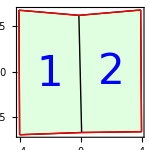

```mathematica
q=RandomizeTemplate[TemplateRectangular[{-4,4, 4},{-2, 2, 4}],.05];
Q=Tissue2DTissue[q];
ShowTissue[Q, "CellNumbers"-> True, 
"CellNumberStyle"-> {Blue,42}, "BoundaryStyle"-> Red,
"Nucleus"-> False, 
Frame-> True,BaseStyle-> {FontSize-> 17}, ImageSize-> 150]
```

## Define the network and the network parameters

```mathematica
network={{A⇄∅,kA, dA}, {pee⇄∅, kP,dP}};
diff={{A, βout, βin, βw}};
pumps={{pee, Fout, Fin}};
parameters={dA->0.1,kA->.1,kP-> .1, dP-> .1, halfwall->.025,DA->700,k->10,μ->1,P->1.5, Fout-> 1, Fin-> 1, βin-> 1, βout-> 1, βw-> 1};
wall={{A-> ∅, kA}};
```

## Run the simulation

simdir = /Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Snapshot0001.png

Actual Clock Time:  | 14-Jun-2017-at-13:03:53
Memory in Use (GB):  | 0.130899
Max Memory Used (GB):  | 0.135849
Free Memory (GB):  | 1.10605

L1 Anticlinal division:Cell 2

Cell 2 (static cell 2) divides at t = 1.6259

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Snapshot0002.png

Actual Clock Time:  | 14-Jun-2017-at-13:03:54
Memory in Use (GB):  | 0.137823
Max Memory Used (GB):  | 0.141037
Free Memory (GB):  | 1.09449
CPU Used(seconds):  | 1.34372
Number of Cells:  | 3
Cell Divisions:  | 1
Simulator Steps:  | 2
Number of Variables:  | 67

L1 Anticlinal division:Cell 1

Cell 1 (static cell 1) divides at t = 2.04784

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Snapshot0003.png

Actual Clock Time:  | 14-Jun-2017-at-13:03:55
Memory in Use (GB):  | 0.139005
Max Memory Used (GB):  | 0.145081
Free Memory (GB):  | 1.09795
CPU Used(seconds):  | 2.67046
Number of Cells:  | 4
Cell Divisions:  | 2
Simulator Steps:  | 3
Number of Variables:  | 97

L1 Anticlinal division:Cell 3

Cell 3 (static cell 3) divides at t = 3.10426

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Snapshot0004.png

Actual Clock Time:  | 14-Jun-2017-at-13:03:57
Memory in Use (GB):  | 0.140636
Max Memory Used (GB):  | 0.145081
Free Memory (GB):  | 1.09559
CPU Used(seconds):  | 4.23893
Number of Cells:  | 5
Cell Divisions:  | 3
Simulator Steps:  | 4
Number of Variables:  | 127

L1 Anticlinal division:Cell 1

L1 Anticlinal division:Cell 2

Cell 1 (static cell 1) divides at t = 4.05625

Cell 2 (static cell 2) divides at t = 4.05625

Tissue snapshot written to /Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Snapshot0005.png

Actual Clock Time:  | 14-Jun-2017-at-13:03:58
Memory in Use (GB):  | 0.142097
Max Memory Used (GB):  | 0.145794
Free Memory (GB):  | 1.09207
CPU Used(seconds):  | 6.18024
Number of Cells:  | 7
Cell Divisions:  | 5
Simulator Steps:  | 5
Number of Variables:  | 157

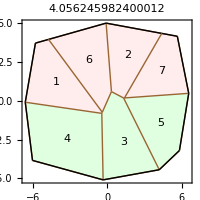

Simulation Completed at t = 4.05625 after 5 cell divisions; Normal Exit. CPU: 6.20758

```mathematica
SIM=grow[Q,0,10,
"Debug"-> False, 
"NDebug"-> False,
"Walls"-> True, 
"TestCase"-> "test", 
"SaveODES"-> True,
"SaveEquations"-> True, 
"MaxDivisions"-> 5, 
"Reactions"-> network, 
"Pumps"-> pumps,
"Diffusion"-> diff, 
"WallReactions"->wall,
 "BoundaryConditions"-> {A-> .1}, 
"Growing"-> True,
"Weights"-> {1,1,0,0},  
"Parameters"-> parameters, 
"DivisionThreshold"-> 25, 
"Verbose"-> False];
```

## Examine the simulation folder

```mathematica
$SIMDIR
```

/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303

```mathematica
Short[ShowSavedFiles[], 5]
```

{/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/DTissue0001.nb,«27»,/Users/mathman/Cellzil…un17-1303/TimeSpans.nb}

```mathematica
ShowSavedFiles["ODE"]
```

{/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/ODES0001.nb,/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/ODES0002.nb,/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/ODES0003.nb,/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/ODES0004.nb}

```mathematica
Short[GetSavedFile[$SIMDIR, "Net",1], 5]
```

/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Network0001.nb

{{A[1]→∅,kA},{∅→A[1],dA},{pee[1]→∅,kP},«108»,{∅→x[6],-0.5 P (y[3][t]-y[5][t])},{∅→y[6],-0.5 P (-x[3][t]+x[5][t])}}

```mathematica
GetSavedFile[$SIMDIR, "Options",1]
```

/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Simulation-Options.nb

{Reactions→{{A⇄∅,kA,dA},{pee⇄∅,kP,dP}},Diffusion→{{A,βout,βin,βw}},Pumps→{{pee,Fout,Fin}},Intercellular→{},k→k,mu→μ,P→P,DivisionModel→Errera,DivisionThreshold→25,DivisionSigma→0.1,DivisionVariable→cell,Weights→{1,1,1},Debug→False,NDebug→False,Walls→True,TestCase→test,SaveODES→True,SaveEquations→True,MaxDivisions→5,WallReactions→{{A→∅,kA}},BoundaryConditions→{A→0.1},Growing→True,Weights→{1,1,0,0},Parameters→{dA→0.1,kA→0.1,kP→0.1,dP→0.1,halfwall→0.025,DA→700,k→10,μ→1,P→1.5,Fout→1,Fin→1,βin→1,βout→1,βw→1},DivisionThreshold→25,Verbose→False}

```mathematica
GetSavedFile[$SIMDIR, "IC",1]
```

/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/IC0001.nb

{DivisionEventFlag→-0.25,CellDivisionThreshold[1]→30.34,CellDivisionThreshold[2]→24.98,A[1]→0.0247599,A[2]→0.0321585,A[1,1]→0.0386505,A[1,2]→0.0482783,A[1,4]→0.0450827,A[1,6]→0.0139225,A[2,3]→0.0332997,A[2,4]→0.0425539,A[2,5]→0.0121552,A[2,7]→0.0481728,pee[1]→0.0293915,pee[2]→0.03689,pee[1,1]→0.0434644,pee[1,2]→0.0158269,pee[1,4]→0.0190006,pee[1,6]→0.0241677,pee[2,3]→0.0233648,pee[2,4]→0.00790483,pee[2,5]→0.0221282,pee[2,7]→0.0449608,x[1]→-4.01822,x[2]→0.0605339,x[3]→3.9997,x[4]→-4.06075,x[5]→-0.120645,x[6]→3.94239,y[1]→-2.08033,y[2]→-2.00661,y[3]→-1.98067,y[4]→2.02623,y[5]→1.85676,y[6]→2.03319,cell[1]→15.9721,cell[2]→15.7709,tip[1]→3.94239,tip[2]→2.03319,ell[1]→4.07942,ell[2]→4.10678,ell[3]→3.93925,ell[4]→3.86762,ell[5]→4.01427,ell[6]→3.94375,ell[7]→4.06686,ellX[1]→-4.07875,ellX[2]→0.0425349,ellX[3]→-3.93916,ellX[4]→0.181179,ellX[5]→0.0573095,ellX[6]→-3.94011,ellX[7]→-4.06303,ellY[1]→-0.0737203,ellY[2]→-4.10656,ellY[3]→-0.0259397,ellY[4]→-3.86338,ellY[5]→-4.01386,ellY[6]→0.169467,ellY[7]→-0.176428,resting[1]→4.07942,resting[2]→4.10678,resting[3]→3.93925,resting[4]→3.86762,resting[5]→4.01427,resting[6]→3.94375,resting[7]→4.06686}

```mathematica
GetSavedFile[$SIMDIR, "Lineage",1]
```

/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Lineage.nb

{0→1,0→2,2→3,1→4,3→5,1→6,2→7}

```mathematica
Short[GetSavedFile[$SIMDIR, "Net",1]]
```

/Users/mathman/Cellzilla/Simulations-14-Jun-17/test-14Jun17-1303/Network0001.nb

{{A[1]→∅,kA},«111»,{∅→y[6],«1»}}